## Studying the Energy Function in terms of its extreme points

Get the minium and the maximum value for the Energy Function of the triaxial rotor at a given spin.

## Expression of the energy function

```mathematica
IF[X_]:=1/(2*X);
A1=IF[72];
A2=IF[15];
A3=IF[7];
V=2.1;
γ=22*π/180;
j=13/2;
H[I_,θ_,φ_,A1_,A2_,A3_,V_,γ_]:=I/2(A1+A2)+A3*I^2+I(I-1/2)Sin[θ]^2(A1*Cos[φ]^2+A2*Sin[φ]^2-A3)+j/2(A2+A3)+A1*j^2-2A1*I*j*Sin[θ]-V*(2j-1)/(j+1)Sin[γ+π/6];
```

## Find the extremal points

```mathematica
max[spin_]:=FindMaximum[{H[spin1,x,y,A1,A2,A3,V,γ],x≥0&&x≤π&&y≥0&&y≤2π},{x,y}][[1]];
min[spin_]:=FindMinimum[{H[spin1,x,y,A1,A2,A3,V,γ],x≥0&&x≤π&&y≥0&&y≤2π},{x,y}][[1]];
MINMAX[spin_]:={min[spin],max[spin]};
```

### Customize template

```mathematica
customize[item_]:=Style[item,19,Bold,Black,FontFamily->"Times New Roman"];
```

```mathematica
table[spin_]:=Grid[{{customize[StringTemplate["V_min"][]],customize[StringTemplate["V_max"][]]},{customize[MINMAX[spin][[1]]],customize[MINMAX[spin][[2]]]}},Frame->All,Background->{None,{LightBlue,LightGreen}}];
table[12.5]
```

V_min | V_max
-1.40248 | 9.39861

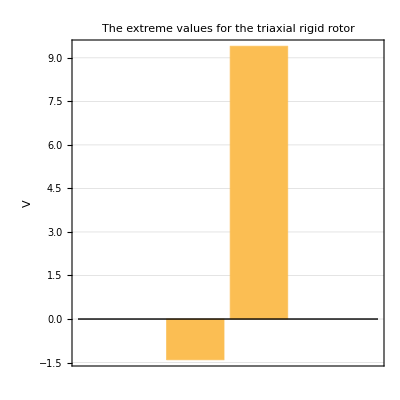

```mathematica
diff[spin_]:=BarChart[{MINMAX[spin][[1]],MINMAX[spin][[2]]},Frame->True,Axes->True,PlotTheme->"Detailed",FrameLabel->{"","V"},AspectRatio->1,PlotLabel->customize["The extreme values for \n the triaxial rigid rotor"]];
diff[12.5]
```